## BeamNG Simulation data

```mathematica
simulation=Import[FileNameJoin[{NotebookDirectory[],"simulation.full.json"}], "RawJSON"];
simulation//Keys
simulation[["records"]]//First//Keys
```

{params,info,road,records}

{timer,pos,dir,vel,steering,steering_input,brake,brake_input,throttle,throttle_input,wheelspeed,vel_kmh,is_oob,oob_counter,max_oob_percentage,oob_distance}

```mathematica
SchemaEdges[d_,p_:"<root>"]:=
If[
ListQ[d],
Sow[p->StringJoin[p,".<list>"]];
Map[SchemaEdges[#,StringJoin[p,".<list>"]]&,d],
If[
AssociationQ[d],
KeyValueMap[
Function[{k,v},
kid=StringJoin[p,".",ToString[k]];
Sow[p->kid];
SchemaEdges[v,kid]],
d
],
Null
]
];
TreePlot[
DeleteDuplicates@First@Last@Reap[SchemaEdges[simulation]],
PlotTheme->"ClassicLabeled"
]
```

-Graphics-

### Convenience functions

```mathematica
RoadNodes[s_]:=s[["road","nodes",All,{1,2}]]
CarPositions[s_]:=s[["records",All,"pos",{1,2}]]
```

### Timestamped scalar data

```mathematica
CarRecord[s_,name_]:=s[["records", All, name]]
TimestampedCarRecord[s_,name_]:=Values/@s[["records", All, {"timer",name}]]
(* Add timestamp to a list of values
	{1, 2, 3, ...} -> {{0, 1}, {0.1, 2}, {0.4, 3}, ...}
 *)
Timestamped[s_,l_]:=Transpose[{s[["records", All, "timer"]],l}]
```

### Visualization functions

```mathematica
PlotCarTrajectory[s_]:=ListLinePlot[{
Legended[RoadNodes[s],"Road"],
Legended[CarPositions[s],"Car"]
}]
```

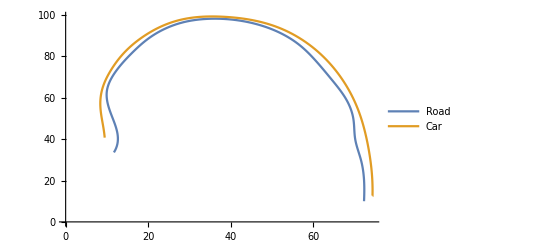

```mathematica
PlotCarTrajectory[simulation]
```

```mathematica
PlotCarDeviation[s_]:=Module[{minDistanceToRoad,velocity},
minDistanceToRoad=Timestamped[
simulation,
Map[
Function[p,Min[EuclideanDistance[p,#]&/@RoadNodes[simulation]]],
CarPositions[simulation]
]
];
velocity=Timestamped[
simulation,
Norm/@CarRecord[simulation,"vel"]
];
ListLinePlot[{
Labeled[TimestampedCarRecord[simulation,"oob_distance"],"oob_distance"],
Labeled[minDistanceToRoad,"Min distance to road"],
Labeled[velocity,"Velocity"]
}]
]
```

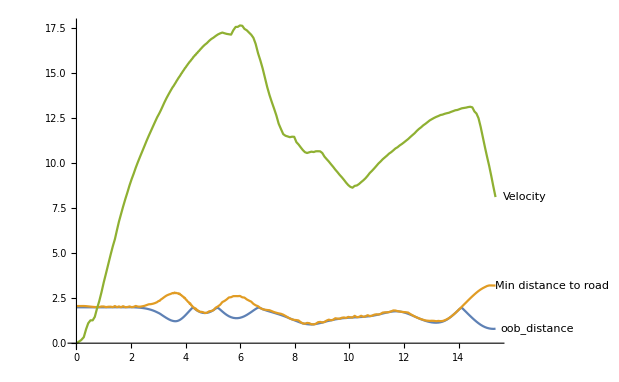

```mathematica
PlotCarDeviation[simulation]
```